```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/2.5.1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f2.xlsx}

```mathematica
file1 = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f1.xlsx

```mathematica
(raw = Import[file1])//TableForm
```

T
sigma
в | 299.6
64.4413
1.54748 | 305.4
62.9813
1.51584 | 310.3
61.9384
1.49119 | 315.3
60.0612
1.44681 | 320.2
58.3926
1.4128 | 325.2
56.5154
1.36017 | 330.
54.0124
1.31413

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
dataset=makeDataset[raw⟦1⟧][SortBy[#T&]]
```

Dataset[<>]

```mathematica
datasetWithErrs=dataset[All,<|"T"->"T","sigma"->(Around[#sigma,#в]&)|>]
```

Dataset[<>]

```mathematica
line=LinearModelFit[Normal@dataset[All,{"T","sigma"}/*Values],{1,x},x]
line["ParameterTable"]
```

FittedModel[166.492-0.338668 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 166.492 | 6.31426 | 26.3676 | 1.46649×10^-6
x | -0.338668 | 0.020026 | -16.9114 | 0.0000132211

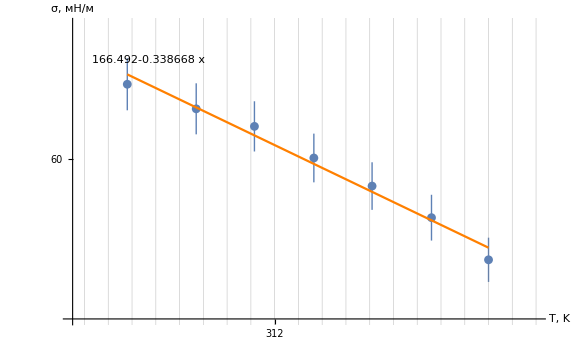

```mathematica
Show[
datasetWithErrs[
ListPlot[#,
AxesLabel->{Style["T, K",Medium],Style["σ, мН/м",Medium]},
AxesStyle->Directive[Arrowheads[{0.025}],Black], 
ImageSize->Large,GridLines->{Range[296,400,2], Range[0,70,1]},
Ticks-> {Range[200,400,4],Range[0,80,2]}, 
PlotRange->{{295,334},{50.5,68}}]
&], 
Plot[line@x,{x,dataset[1,"T"],dataset[-1,"T"]}, 
PlotLabels->Placed[line@x,Above],
PlotStyle->Orange]
]
```